```mathematica
￿
```

```mathematica
Clear["Global`*"]
```

x[t]→C[2]-(c^2 m_0)/(f √(Sec[C[1]+(f t)/(c m_0)]^2))

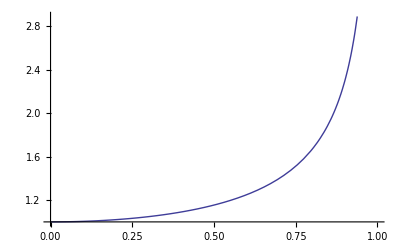

```mathematica
γ[v_]:=1/(√(1-v^2/c^2))
sol=DSolve[x''[t]==f/(Subscript[m, 0] γ[x'[t]]),x[t],t][[1,1]]
Plot[γ[v]/.c->1,{v,0,1}]
```

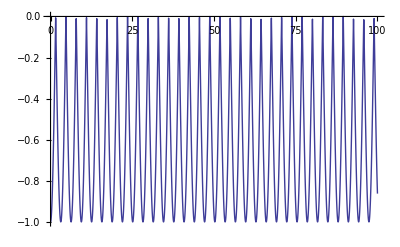

```mathematica
Plot[x[t]/.{sol}/.{C[2]->0,C[1]->0,c->1,f->1,Subscript[m, 0]->1},{t,0,100}]
```

Instead, Start with the known hyperbolic function and determine how to position it correctly to match any initial conditions we want.

```mathematica
Clear["Global`*"]
```

Add in factors A and B to allow freedom in x and t

```mathematica
x[t_]:=√(c^2 (t+A)^2+c^4/α^2)+B
```

Solve for A and B given that we know the position and speed at time t_0

```mathematica
sol=FullSimplify[Solve[{x[Subscript[t, 0]]==Subscript[x, 0],x'[Subscript[t, 0]]==Subscript[v, 0]},{A,B}],{}]
```

{{B→-√(c^6/(α^2 (c^2-v_0^2)))+x_0,A→-t_0-(c^2 v_0^2)/(√(c^2 α^2 v_0^2 (c^2-v_0^2)))},{B→-√(c^6/(α^2 (c^2-v_0^2)))+x_0,A→-t_0+(c^2 v_0^2)/(√(c^2 α^2 v_0^2 (c^2-v_0^2)))}}

Here is the formula for dx(dt, α, v_0)

```mathematica
FullSimplify[x[Subscript[t, 0]+dt]-Subscript[x, 0]/.sol[[2]]]
```

-√(c^6/(α^2 (c^2-v_0^2)))+√(c^4/α^2+c^2 (dt+(c^2 v_0^2)/(√(c^2 α^2 v_0^2 (c^2-v_0^2))))^2)

And the formula for v_1(dt,α,v_0)

```mathematica
FullSimplify[x'[Subscript[t, 0]+dt]/.sol[[2]]]
```

(c^2 (dt+(c^2 v_0^2)/(√(c^2 α^2 v_0^2 (c^2-v_0^2)))))/(√(c^4/α^2+c^2 (dt+(c^2 v_0^2)/(√(c^2 α^2 v_0^2 (c^2-v_0^2))))^2))

Show that it works:

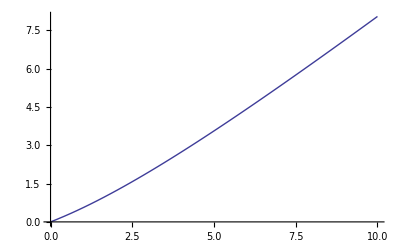

```mathematica
params={α->-0.2,Subscript[v, 0]->-0.5,Subscript[x, 0]->0,Subscript[t, 0]->0,c->1};
Plot[x[t]/.sol[[2]]/.params,{t,0,10}]
```

Above equation fails whan v_0=0, so we'll need another for that case:

```mathematica
sx[t_]:=Simplify[Limit[x[t]/.sol[[2]],Subscript[v, 0]->0]]
```

```mathematica
FullSimplify[sx[Subscript[t, 0]+dt]-Subscript[x, 0]/.sol[[2]]]
FullSimplify[sx'[Subscript[t, 0]+dt]/.sol[[2]]]
```

√(c^2 dt^2+c^4/α^2)-√(c^4/α^2)

(c^2 dt)/(√(c^2 dt^2+c^4/α^2))

```mathematica
x[t]/.sol[[1]]/.params
```

-5.7735+√(25.+(-2.88675+t)^2)

Another try:

```mathematica
Clear["Global`*"]
```

```mathematica
κ:=g/c^2
γ[τ_]:=√(1+(κ τ)^2)
β[τ_]:=(κ τ)/γ[τ]
```

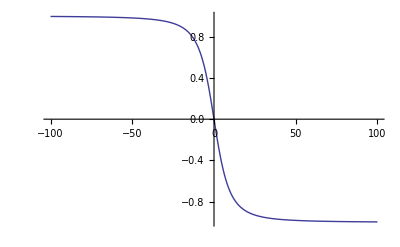

```mathematica
Plot[β[t]/.{g->-.1,c->1},{t,-100,100},PlotRange->All]
```

```mathematica
sol=Simplify[Solve[β[Subscript[t, 0]]==Subscript[v, 0],Subscript[t, 0]]]
```

{{t_0→-(c^2 v_0)/(√(-g^2 (-1+v_0^2)))},{t_0→(c^2 v_0)/(√(-g^2 (-1+v_0^2)))}}

Note: use solution 1 if g<0, otherwise use 2

```mathematica
FullSimplify[β[Subscript[t, 0]+dt]/.sol[[1]]]
FullSimplify[β[Subscript[t, 0]+dt]/.sol[[2]]]
```

(g (dt-(c^2 v_0)/(√(-g^2 (-1+v_0^2)))))/(c^2 √(1+(g^2 (dt-(c^2 v_0)/(√(-g^2 (-1+v_0^2))))^2)/c^4))

(g (dt+(c^2 v_0)/(√(-g^2 (-1+v_0^2)))))/(c^2 √(1+(g^2 (dt+(c^2 v_0)/(√(-g^2 (-1+v_0^2))))^2)/c^4))

```mathematica
x[τ_]:=(√(1+(κ τ)^2))/κ+A
```

```mathematica
xsol=FullSimplify[Solve[x[Subscript[t, 0]]==Subscript[x, 0],A]]
```

{{A→-(c^2 √(1+(g^2 t_0^2)/c^4))/g+x_0}}

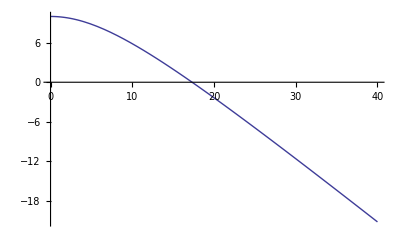

```mathematica
Plot[{x[Subscript[t, 0]+dt]}/.xsol[[1]]/.sol[[1]]/.{g->-0.1,c->1,Subscript[x, 0]->10,Subscript[v, 0]->-0.},{dt,0,40}]
```

```mathematica
FullSimplify[x[Subscript[t, 0]+dt]/.xsol[[1]]/.sol[[1]],{c∈Reals,t∈Reals,g∈Reals,Subscript[x, 0]∈Reals,Subscript[v, 0]∈Reals}]
```

(-c^2 √(1/(1-v_0^2))+c^2 √(1+(g^2 (dt-(c^2 v_0)/(√(-g^2 (-1+v_0^2))))^2)/c^4)+g x_0)/g